```mathematica
myParetoListData = Sort[{25, 50, 10, 77, 8, 13, 43}];
myParetoListDataDesc = Sort[myParetoListData, Greater];
myParetoListDataPercent =ConstantArray[0, Length[myParetoListData] + 1];
myCounter = 1;

While[myCounter <= Length[myParetoListData],
myParetoListDataPercent[[myCounter + 1]] = (Total[Take[myParetoListData,
{1, myCounter}]]*100)/ Total[myParetoListData];
myCounter++;
];
```

```mathematica
N[myParetoListDataPercent] (* NOTE: Use N[result] to get real numbers and not fractions *)
```

{0.,3.53982,7.9646,13.7168,24.7788,43.8053,65.9292,100.}

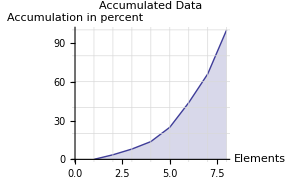

```mathematica
ListLinePlot[myParetoListDataPercent,
AxesLabel->{"Elements", "Accumulation in percent"},
GridLines->{Range[1, Length[myParetoListDataPercent]],
Range[0, Max[myParetoListDataPercent], 20]},
PlotLabel->"Accumulated Data",
GridLinesStyle->LightGray, Filling -> Axis]
```

```mathematica
myNumbers = {50, 50, 25};
myAverage = (1/Length[myNumbers]) * Total[myNumbers]
```

125/3

```mathematica
N[myAverage]
```

41.6667

```mathematica
(* NOTE: Remember semicolon after everything but last statement! *)
myStdDev[n0_]:=
Module[{myArray=n0},
tempNum = 0;
For [i=1, i<=Length[myArray], i++,
	tempNum=tempNum+((myArray[[i]]-Mean[myArray])^2)
];
	If [Length[myArray]>1,
		Sqrt[(1/(Length[myArray]-1))*tempNum],
		0
]
]
(* Test it... *)
{myStdDev[{25, 50, -50}], N[myStdDev[{25, 50, -50}]]}
```

{25 √(13/3),52.0416}

```mathematica
{StandardDeviation[{50, -50, 25}], N[StandardDeviation[{50, -50, 25}]]}
```

{25 √(13/3),52.0416}

```mathematica
(* This is a custom module *)
myModule[x0_, y0_] := Module[{x = x0, y = y0},x = x + 2; y = y * 10; x + y]
```

```mathematica
myModule[5, 15]
```

157

```mathematica
(* Define a custom function *)
myFunction[x_] := 3 x^2 + 2x+7;
(* Test the custom function *)
myFunction[1.6]
```

17.88

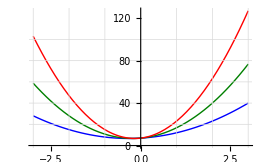

```mathematica
(* Plot the custom function *)
Plot[{myFunction[x], myFunction[1.5x], myFunction[2x]},
{x, -3, 3},
PlotStyle->{RGBColor[0, 0, 1], RGBColor[0, 0.5, 0],
RGBColor[1, 0, 0]},
Filling->None, Axes->True,
GridLines->{Range[-3,3], Range[0, 100, 20]},
GridLinesStyle->LightGray]
```

```mathematica
(* Create a table fro the custom function *)
Table[myFunction[i], {i, -5, 5, 2}]
```

{72,28,8,12,40,92}

```mathematica
(* Map values to the custom function *)
myValueList = {3, 4, 7, 2, 9, 21};
Map[myFunction, myValueList]
```

{40,63,168,23,268,1372}

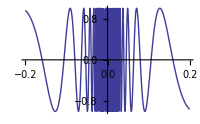

```mathematica
Plot[Sin[1/x], {x, -0.2, 0.2}] (* Limit x->0 *)
```

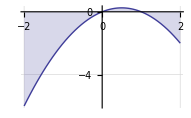

```mathematica
Plot[x - x^2, {x, -2, 2}, GridLines->Automatic,
GridLinesStyle->LightGray, Filling -> Axis]
```

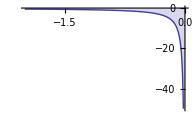

```mathematica
Plot[x^-1, {x, -2, 0}, PlotRange->{{-2,0}, {0, -50}},
Filling -> Axis]
```

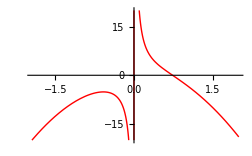

```mathematica
Plot[(5 x^4-2x)/-x^2, {x, -2, 2}, Filling -> None, PlotStyle->Red,
PlotRange->{{-2,2}, {20, -20}}]
```

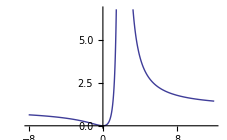

```mathematica
Plot[x^2/(x-2)^2, {x, -8, 12}, Filling -> None]
```

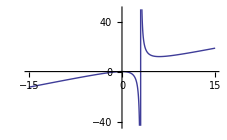

```mathematica
Plot[x^2/(x-3), {x, -15, 15}, Filling -> None]
```

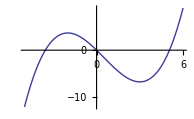

```mathematica
Plot[x^3/6-x^2/4-3x, {x,-5, 6}, Filling -> None]
```

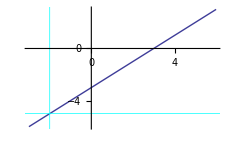

```mathematica
Plot[(x^2-x-6)/(x+2), {x,-3, 6}, GridLines->{{-2}, {-5}},GridLinesStyle->Cyan] 
(* Function has a "hole" at (-2,-5). It gives 0/0 *)
```

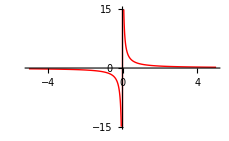

```mathematica
(* Reciprocal. The reciprocal function: y=1⁄x.
For every x except 0, y represents its multiplicative inverse. *)
Plot[1/x, {x,-5, 5}, GridLines ->None, Filling -> None,PlotStyle->Red,
PlotRange->{{-5,5}, {-15,15}}]
```